-Graphics-

-Graphics-

-Graphics3D-

-Graphics-

-Graphics-

-Graphics3D-

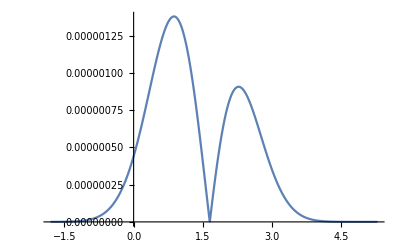

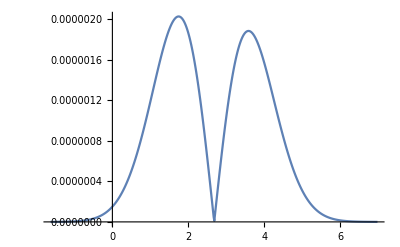

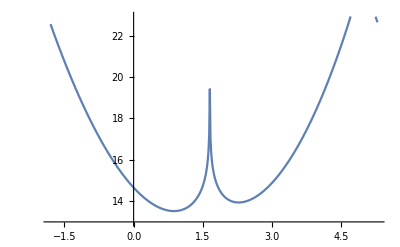

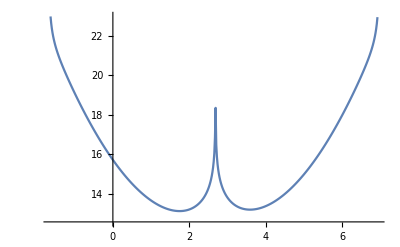

-Graphics-

-Graphics3D-

-Graphics-

-Graphics3D-

```mathematica
{xi,xf,dx}={-1.8161097383568912,5.275605000228945,0.013878111034414553};
{yi,yf,dy}={-1.6463063667992741,6.966334661866419,0.016854483422046367};
nbins=512;
kde=ToExpression[StringSplit[StringReplace[ReadList["kde.out",String],{"e+":>"*^","e-":>"*^-"}]]];
kde=Chop[kde];
fes=-Log[kde];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,kde[[i,j]]},{i,nbins},{j,nbins}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotLegends->Automatic,PlotRange->{domain[[1]],domain[[2]],Full},Contours->10(*,AspectRatio->(4.1+1.5)/(3.4+1.5)*)]
```